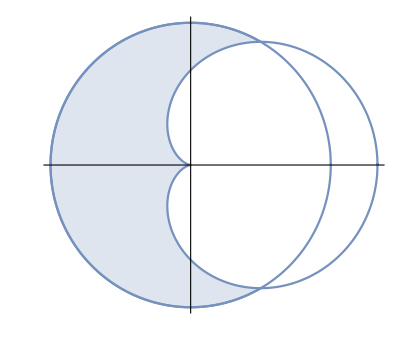

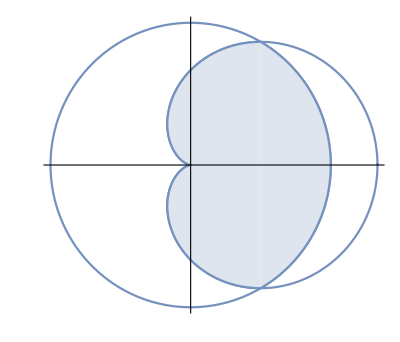

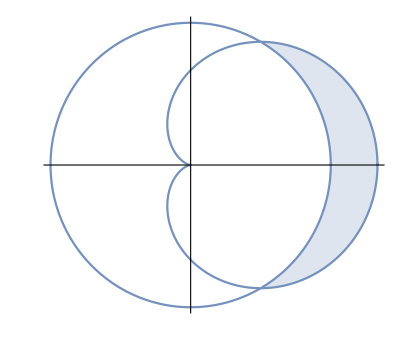

```mathematica
r[t_]:=3;
r2[t_]:=2(1+Cos[t]);
x[t_]:=r[t] Cos[t];
y[t_]:=r[t]Sin[t];
x2[t_]:=r2[t] Cos[t];
y2[t_]:=r2[t]Sin[t];

shadecolor=RGBColor[223/256,230/256,240/256,1];
linecolor = RGBColor[117/256,147/256,191/256,1];
shadecolor2=RGBColor[1,1,1,1];

BlueCirc=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
WhiteCirc=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor2,Polygon[l]},{linecolor,Line[l]}};
ClearCirc=ParametricPlot[{x[t],y[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{Transparent,Polygon[l]},{linecolor,Line[l]}};
BlueCard=ParametricPlot[{x2[t],y2[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
WhiteCard=ParametricPlot[{x2[t],y2[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor2,Polygon[l]},{linecolor,Line[l]}};
BlueSliver=ParametricPlot[{x2[t],y2[t]},{t,Pi/3,5Pi/3},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
BlueSliver2=ParametricPlot[{x[t],y[t]},{t,-Pi/3,Pi/3},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor,Polygon[l]},{linecolor,Line[l]}};
WhiteSliver=ParametricPlot[{x2[t],y2[t]},{t,5Pi/3,Pi/3},Ticks->None,PlotRange->All]/.Line[l_List]:>{{shadecolor2,Polygon[l]},{linecolor,Line[l]}};
ClearCard=ParametricPlot[{x2[t],y2[t]},{t,0,2Pi+0.01},Ticks->None,PlotRange->All]/.Line[l_List]:>{{Transparent,Polygon[l]},{linecolor,Line[l]}};

Show[BlueCirc,WhiteCard,ClearCirc]
Show[WhiteCirc,ClearCard,BlueSliver,BlueSliver2]
Show[BlueCard,WhiteCirc,WhiteSliver]
```

```mathematica
R1=3;
R2=2(1+Cos[t]);

a=Pi/3;
b=5Pi/3;
b2=-Pi/3;

circle=Integrate[1/2(R1^2),{t,0,2Pi}];
cardioid=Integrate[1/2(R2^2),{t,0,2Pi}];

left=Integrate[1/2(R1^2-R2^2),{t,a,b}]
middle=cardioid-sliver
sliver=Integrate[1/2(R2^2-R1^2),{t,b2,a}]

tot1=left+middle+sliver
tot2=circle+sliver
```

(9 √3)/2+2 π

-(9 √3)/2+7 π

(9 √3)/2-π

(9 √3)/2+8 π

(9 √3)/2+8 π

```mathematica
(*http://tutorial.math.lamar.edu/Classes/CalcII/PolarArea.aspx*)
```